#### Valores experimentales de eritrocitos

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
```

```mathematica
datos0Im=Import["C:\\Users\\Poh\\Documents\\Tesis\\Refractive index\\28.7_k_ImN_Erythrocytes.csv"];
datos0Re=Import["C:\\Users\\Poh\\Documents\\Tesis\\Refractive index\\28.7_n_ReN_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1Im=Drop[datos0Im,1];
datos1Re=Drop[datos0Re,1];
datos2Im=h c/datos1Im[[All,1]];
datos2Re=h c/datos1Re[[All,1]];
(*Se interpolan los datos de la parte imaginaria*)
parteIm=Interpolation[Transpose[{datos2Im,datos1Im[[All,2]]}]]
parteRe=Interpolation[Transpose[{datos2Re,datos1Re[[All,2]]}]]
(*Se toma a la primera columna como el vector de energía*)
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
Export["parteIm.csv",Transpose[{energias,parteIm1}]]
```

parteIm.csv

```mathematica
Export["parteRe.csv",Transpose[{energias,parteRe1}]]
```

parteRe.csv

```mathematica
eps1[x_]:=parteRe[x]^2-parteIm[x]^2;
eps2[x_]:=(2*parteRe[x]*parteIm[x]);
```

```mathematica
parteIm1=Table[eps2[x],{x,1.19,4.82,0.01}];
parteRe1=Table[eps1[x],{x,1.19,4.82,0.01}];
energias=Range[1.19,4.82,0.01];
```

```mathematica
Export["parteIm.csv",Transpose[{energias,parteIm1}]]
```

parteIm.csv

```mathematica
Export["parteRe.csv",Transpose[{energias,parteRe1}]]
```

parteRe.csv

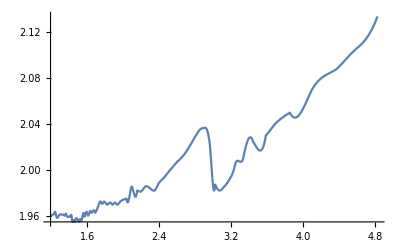

```mathematica
Plot[{eps1[x]},{x,1.19,4.83}]
```

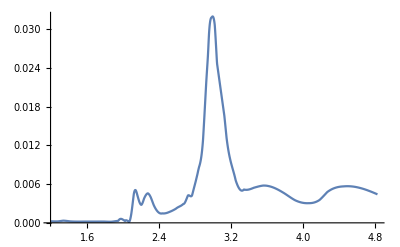

```mathematica
Plot[{eps2[x]},{x,1.19,4.83},PlotRange->All]
```